```mathematica
data=Transpose[Import["C:\\Users\\Abigail\\Desktop\\Wolfram data\\Trematode\\Data_trematode_new.csv"]];Dimensions[data]
```

{7,211}

```mathematica
trematode12S=data[[2,2;;211]]
trematode16S=data[[3,2;;211]]
trematodeCOI=data[[4,2;;211]]
trematodeCOII=data[[5,2;;211]]
trematodecytb=data[[6,2;;211]]
trematodeND=data[[7,2;;211]]
```

{0.127,0.147,0.103,0.129,0.217,0.219,0.079,0.164,0.188,0.136,0.149,0.123,0.105,0.09,0.094,0.066,0.166,0.204,0.116,0.201,0.131,0.208,0.21,0.21,0.21,0.208,0.197,0.212,0.236,0.287,0.287,0.298,0.26,0.317,0.302,0.298,0.256,0.252,0.252,0.197,0.206,0.23,0.234,0.234,0.225,0.239,0.249,0.212,0.223,0.236,0.241,0.282,0.322,0.324,0.267,0.291,0.289,0.269,0.295,0.293,0.267,0.3,0.291,0.306,0.306,0.337,0.309,0.309,0.313,0.309,0.293,0.293,0.293,0.289,0.304,0.295,0.289,0.304,0.302,0.324,0.3,0.3,0.302,0.295,0.278,0.276,0.282,0.289,0.291,0.306,0.313,0.333,0.324,0.348,0.335,0.337,0.337,0.322,0.324,0.317,0.306,0.33,0.311,0.306,0.311,0.298,0.309,0.335,0.306,0.306,0.322,0.324,0.295,0.298,0.284,0.3,0.313,0.319,0.326,0.274,0.306,0.324,0.269,0.278,0.276,0.284,0.287,0.263,0.265,0.263,0.278,0.3,0.3,0.28,0.315,0.298,0.282,0.271,0.271,0.274,0.293,0.267,0.263,0.271,0.298,0.317,0.313,0.28,0.284,0.309,0.291,0.298,0.309,0.298,0.282,0.28,0.269,0.274,0.326,0.33,0.344,0.276,0.276,0.282,0.256,0.295,0.302,0.306,0.271,0.265,0.263,0.247,0.3,0.287,0.298,0.306,0.309,0.313,0.284,0.315,0.319,0.317,0.271,0.26,0.26,0.245,0.311,0.3,0.289,0.269,0.263,0.267,0.243,0.319,0.309,0.298,0.287,0.278,0.287,0.271,0.317,0.295,0.313,0.295,0.291,0.276,0.267,0.322,0.319,0.33}

{0.144,0.151,0.101,0.162,0.259,0.24,0.08,0.143,0.147,0.155,0.18,0.174,0.113,0.122,0.129,0.071,0.162,0.201,0.107,0.166,0.113,0.169,0.153,0.147,0.14,0.162,0.206,0.215,0.215,0.269,0.258,0.246,0.233,0.24,0.231,0.242,0.235,0.253,0.241,0.25,0.251,0.26,0.242,0.247,0.246,0.231,0.24,0.195,0.195,0.209,0.2,0.289,0.3,0.298,0.272,0.269,0.263,0.281,0.286,0.285,0.278,0.285,0.281,0.312,0.278,0.316,0.313,0.303,0.314,0.298,0.271,0.269,0.284,0.278,0.291,0.32,0.323,0.28,0.269,0.299,0.299,0.29,0.304,0.296,0.271,0.256,0.268,0.264,0.277,0.299,0.298,0.271,0.263,0.299,0.296,0.289,0.304,0.295,0.265,0.254,0.253,0.258,0.284,0.305,0.303,0.289,0.268,0.299,0.296,0.285,0.304,0.295,0.26,0.263,0.251,0.271,0.276,0.295,0.286,0.285,0.263,0.293,0.274,0.268,0.291,0.278,0.259,0.251,0.255,0.264,0.274,0.294,0.286,0.294,0.305,0.29,0.281,0.282,0.3,0.303,0.276,0.265,0.269,0.268,0.299,0.318,0.312,0.28,0.276,0.293,0.299,0.293,0.316,0.304,0.242,0.247,0.262,0.263,0.287,0.29,0.298,0.296,0.276,0.274,0.289,0.302,0.33,0.331,0.291,0.268,0.277,0.287,0.289,0.294,0.289,0.304,0.265,0.276,0.272,0.318,0.299,0.295,0.305,0.28,0.293,0.311,0.305,0.307,0.303,0.298,0.277,0.293,0.312,0.285,0.3,0.294,0.311,0.286,0.313,0.314,0.308,0.316,0.322,0.298,0.29,0.289,0.303,0.295,0.308,0.307}

{0.176,0.165,0.154,0.171,0.237,0.221,0.089,0.133,0.125,0.184,0.195,0.166,0.141,0.139,0.142,0.092,0.108,0.213,0.164,0.207,0.159,0.213,0.222,0.215,0.223,0.16,0.169,0.177,0.242,0.268,0.27,0.264,0.272,0.255,0.273,0.26,0.264,0.222,0.238,0.194,0.201,0.208,0.223,0.201,0.197,0.217,0.211,0.213,0.202,0.219,0.223,0.326,0.318,0.316,0.282,0.286,0.296,0.289,0.294,0.299,0.291,0.298,0.294,0.298,0.3,0.3,0.291,0.281,0.296,0.292,0.318,0.29,0.293,0.294,0.306,0.313,0.305,0.293,0.3,0.3,0.284,0.29,0.294,0.299,0.317,0.281,0.286,0.29,0.303,0.302,0.315,0.302,0.308,0.281,0.29,0.282,0.29,0.294,0.301,0.286,0.288,0.291,0.308,0.31,0.315,0.301,0.3,0.292,0.296,0.282,0.29,0.295,0.309,0.292,0.298,0.307,0.306,0.308,0.303,0.268,0.267,0.27,0.245,0.239,0.255,0.262,0.282,0.253,0.264,0.252,0.279,0.294,0.287,0.268,0.277,0.278,0.268,0.265,0.272,0.267,0.286,0.253,0.259,0.251,0.301,0.319,0.313,0.295,0.304,0.305,0.282,0.29,0.298,0.299,0.294,0.274,0.283,0.286,0.315,0.324,0.326,0.302,0.272,0.264,0.264,0.302,0.306,0.304,0.31,0.271,0.271,0.26,0.297,0.29,0.298,0.304,0.281,0.268,0.27,0.305,0.307,0.316,0.288,0.249,0.252,0.24,0.268,0.288,0.276,0.287,0.243,0.246,0.238,0.262,0.272,0.274,0.278,0.252,0.255,0.249,0.278,0.278,0.275,0.294,0.254,0.262,0.25,0.278,0.277,0.277}

{0.179,0.204,0.177,0.161,0.349,0.339,0.113,0.179,0.17,0.183,0.208,0.183,0.177,0.149,0.165,0.159,0.217,0.19,0.181,0.192,0.194,0.217,0.199,0.199,0.185,0.226,0.299,0.326,0.292,0.317,0.303,0.328,0.294,0.328,0.314,0.36,0.289,0.333,0.281,0.274,0.285,0.296,0.292,0.294,0.303,0.303,0.29,0.337,0.337,0.355,0.348,0.409,0.414,0.427,0.371,0.396,0.414,0.366,0.38,0.394,0.38,0.394,0.409,0.366,0.36,0.384,0.378,0.366,0.378,0.367,0.376,0.357,0.351,0.353,0.371,0.387,0.391,0.38,0.382,0.407,0.375,0.371,0.391,0.373,0.409,0.385,0.378,0.36,0.391,0.38,0.384,0.401,0.385,0.384,0.384,0.375,0.382,0.369,0.403,0.384,0.376,0.375,0.391,0.373,0.392,0.4,0.409,0.389,0.371,0.358,0.387,0.392,0.41,0.385,0.384,0.362,0.369,0.38,0.392,0.385,0.403,0.4,0.364,0.348,0.384,0.367,0.378,0.357,0.362,0.337,0.385,0.391,0.391,0.419,0.419,0.428,0.384,0.387,0.401,0.396,0.425,0.384,0.375,0.387,0.421,0.376,0.418,0.419,0.419,0.419,0.412,0.416,0.41,0.425,0.412,0.384,0.391,0.387,0.401,0.405,0.419,0.4,0.371,0.375,0.366,0.398,0.391,0.389,0.421,0.384,0.371,0.382,0.412,0.398,0.398,0.432,0.405,0.412,0.401,0.392,0.423,0.418,0.394,0.369,0.36,0.367,0.387,0.407,0.4,0.403,0.366,0.353,0.36,0.376,0.387,0.384,0.396,0.36,0.362,0.371,0.385,0.409,0.418,0.407,0.371,0.369,0.346,0.369,0.391,0.392}

{0.186,0.172,0.144,0.176,0.246,0.239,0.08,0.168,0.158,0.185,0.22,0.229,0.162,0.162,0.164,0.108,0.181,0.223,0.149,0.217,0.143,0.203,0.205,0.196,0.198,0.219,0.221,0.227,0.256,0.248,0.289,0.254,0.276,0.243,0.258,0.238,0.255,0.228,0.25,0.203,0.207,0.216,0.213,0.208,0.214,0.226,0.202,0.251,0.261,0.262,0.257,0.311,0.306,0.323,0.286,0.281,0.294,0.297,0.282,0.292,0.291,0.295,0.295,0.267,0.289,0.295,0.266,0.257,0.268,0.245,0.313,0.27,0.276,0.272,0.292,0.291,0.298,0.248,0.252,0.288,0.25,0.258,0.263,0.251,0.29,0.277,0.275,0.276,0.289,0.299,0.304,0.23,0.254,0.271,0.25,0.246,0.246,0.241,0.297,0.273,0.256,0.271,0.282,0.283,0.295,0.237,0.251,0.279,0.234,0.239,0.248,0.248,0.284,0.25,0.266,0.277,0.28,0.29,0.294,0.254,0.259,0.288,0.255,0.251,0.266,0.247,0.286,0.264,0.26,0.264,0.296,0.305,0.307,0.27,0.275,0.293,0.268,0.267,0.262,0.267,0.294,0.284,0.293,0.298,0.312,0.312,0.318,0.251,0.281,0.312,0.28,0.278,0.269,0.276,0.307,0.29,0.295,0.308,0.33,0.336,0.335,0.288,0.251,0.226,0.255,0.282,0.266,0.279,0.294,0.254,0.252,0.266,0.288,0.277,0.28,0.302,0.274,0.293,0.297,0.31,0.31,0.307,0.276,0.255,0.245,0.266,0.264,0.266,0.269,0.292,0.25,0.238,0.26,0.26,0.264,0.262,0.297,0.263,0.253,0.271,0.279,0.285,0.292,0.278,0.238,0.25,0.256,0.265,0.264,0.274}

{0.205,0.19,0.157,0.185,0.287,0.302,0.083,0.141,0.141,0.236,0.243,0.24,0.184,0.167,0.172,0.119,0.131,0.229,0.204,0.21,0.204,0.2,0.224,0.172,0.174,0.19,0.285,0.269,0.297,0.293,0.308,0.292,0.292,0.281,0.288,0.294,0.309,0.254,0.265,0.209,0.203,0.217,0.222,0.198,0.215,0.211,0.209,0.281,0.287,0.282,0.293,0.386,0.383,0.377,0.335,0.348,0.329,0.334,0.335,0.316,0.346,0.344,0.338,0.309,0.304,0.341,0.291,0.291,0.292,0.304,0.348,0.331,0.313,0.306,0.359,0.335,0.338,0.29,0.287,0.338,0.259,0.271,0.284,0.281,0.333,0.313,0.297,0.299,0.353,0.331,0.327,0.279,0.28,0.327,0.269,0.265,0.29,0.279,0.347,0.313,0.31,0.309,0.356,0.329,0.312,0.288,0.308,0.348,0.287,0.291,0.292,0.312,0.334,0.338,0.309,0.319,0.364,0.344,0.342,0.257,0.266,0.311,0.241,0.243,0.248,0.253,0.321,0.277,0.253,0.265,0.318,0.316,0.309,0.296,0.282,0.317,0.282,0.275,0.271,0.273,0.313,0.294,0.277,0.282,0.344,0.33,0.323,0.308,0.291,0.354,0.29,0.294,0.291,0.278,0.311,0.313,0.312,0.318,0.377,0.356,0.355,0.329,0.288,0.282,0.286,0.337,0.323,0.321,0.331,0.29,0.278,0.271,0.322,0.318,0.316,0.384,0.341,0.337,0.333,0.373,0.34,0.333,0.328,0.292,0.275,0.297,0.31,0.303,0.29,0.317,0.287,0.278,0.292,0.315,0.277,0.281,0.317,0.287,0.287,0.281,0.308,0.302,0.298,0.343,0.291,0.287,0.305,0.322,0.29,0.286}

```mathematica
Stat[clusterdata_]:={Mean[#],StandardDeviation[#],MinMax[#]}&/@clusterdata
```

```mathematica
PlotCluster[clusterdata_,plotlabel_]:=ListPlot[clusterdata,BaseStyle->{FontFamily->"Times New Roman",FontSize->12},Frame->True,FrameLabel->{"Samples","Genetic Distance"},GridLines->Automatic,ImageSize->Medium,PlotStyle->{{PointSize[Medium],Red},{PointSize[Medium],Green},{PointSize[Medium],Blue},{PointSize[Medium],Orange}},PlotLabel->plotlabel]
```

```mathematica
{clstrtrematode12S,clstrtrematode16S,clstrtrematodeCOI,clstrtrematodeCOII,clstrtrematodecytb,clstrtrematodeND}=FindClusters[#,4,Method->"KMeans"]&/@{trematode12S,trematode16S,trematodeCOI,trematodeCOII,trematodecytb,trematodeND};
```

```mathematica
Stat[clstrtrematode12S]
```

{{0.120313,0.0292568,{0.066,0.166}},{0.22075,0.0173944,{0.188,0.249}},{0.278148,0.0119186,{0.252,0.295}},{0.313059,0.0122701,{0.298,0.348}}}

```mathematica
statdata=Stat/@{clstrtrematode12S,clstrtrematode16S,clstrtrematodeCOI,clstrtrematodeCOII,clstrtrematodecytb,clstrtrematodeND}
```

{{{0.120313,0.0292568,{0.066,0.166}},{0.22075,0.0173944,{0.188,0.249}},{0.278148,0.0119186,{0.252,0.295}},{0.313059,0.0122701,{0.298,0.348}}},{{0.119769,0.0252921,{0.071,0.147}},{0.181667,0.0226586,{0.151,0.215}},{0.26172,0.0135013,{0.231,0.28}},{0.298856,0.0110948,{0.281,0.331}}},{{0.146111,0.0274802,{0.089,0.177}},{0.215407,0.0150799,{0.184,0.24}},{0.266814,0.0113754,{0.242,0.283}},{0.299895,0.0100355,{0.284,0.326}}},{{0.183625,0.0244074,{0.113,0.226}},{0.37116,0.0130675,{0.337,0.387}},{0.30205,0.0169534,{0.274,0.333}},{0.405444,0.0116991,{0.389,0.432}}},{{0.155867,0.0289676,{0.08,0.186}},{0.261484,0.0102447,{0.243,0.279}},{0.221167,0.0138541,{0.196,0.241}},{0.296743,0.0127355,{0.28,0.336}}},{{0.221192,0.0204978,{0.19,0.254}},{0.152167,0.0304208,{0.083,0.185}},{0.290533,0.0138648,{0.257,0.313}},{0.338239,0.0179208,{0.315,0.386}}}}

```mathematica
MySort[clusterdata_]:=Module[{len,max,or},
len=Length@clusterdata;
max=Max/@clusterdata;
or=Ordering[max];
clusterdata[[or]]
];
```

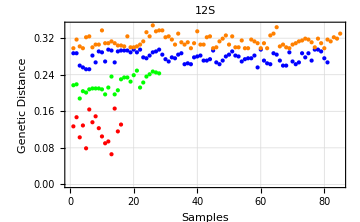

```mathematica
PlotCluster[MySort[clstrtrematode12S],"12S"]
```

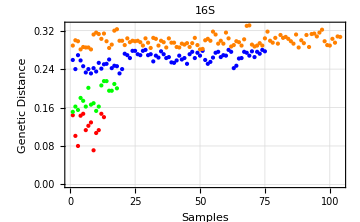

```mathematica
PlotCluster[MySort[clstrtrematode16S],"16S"]
```

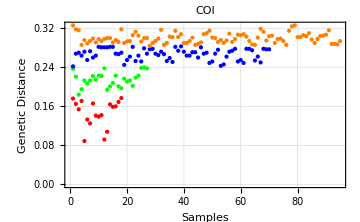

```mathematica
PlotCluster[MySort[clstrtrematodeCOI],"COI"]
```

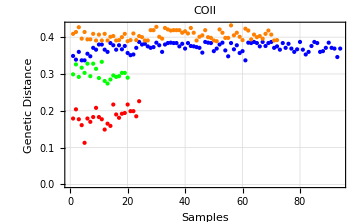

```mathematica
PlotCluster[MySort[clstrtrematodeCOII],"COII"]
```

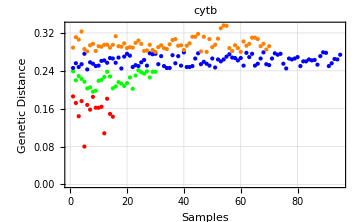

```mathematica
PlotCluster[MySort[clstrtrematodecytb],"cytb"]
```

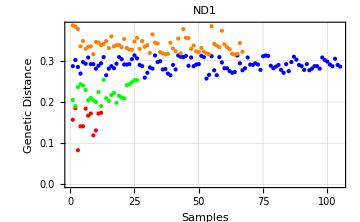

PlotCluster[MySort[{{0.176,0.165,0.154,0.171,0.089,0.133,0.125,0.166,0.141,0.139,0.142,0.092,0.108,0.164,0.159,0.16,0.169,0.177},{0.237,0.221,0.184,0.195,0.213,0.207,0.213,0.222,0.215,0.223,0.222,0.238,0.194,0.201,0.208,0.223,0.201,0.197,0.217,0.211,0.213,0.202,0.219,0.223,0.239,0.24,0.238},{0.242,0.268,0.27,0.264,0.272,0.255,0.273,0.26,0.264,0.282,0.281,0.281,0.281,0.282,0.282,0.268,0.267,0.27,0.245,0.255,0.262,0.282,0.253,0.264,0.252,0.279,0.268,0.277,0.278,0.268,0.265,0.272,0.267,0.253,0.259,0.251,0.282,0.274,0.283,0.272,0.264,0.264,0.271,0.271,0.26,0.281,0.268,0.27,0.249,0.252,0.268,0.276,0.243,0.246,0.262,0.272,0.274,0.278,0.252,0.255,0.249,0.278,0.278,0.275,0.254,0.262,0.25,0.278,0.277,0.277},{0.326,0.318,0.316,0.286,0.296,0.289,0.294,0.299,0.291,0.298,0.294,0.298,0.3,0.3,0.291,0.296,0.292,0.318,0.29,0.293,0.294,0.306,0.313,0.305,0.293,0.3,0.3,0.284,0.29,0.294,0.299,0.317,0.286,0.29,0.303,0.302,0.315,0.302,0.308,0.29,0.29,0.294,0.301,0.286,0.288,0.291,0.308,0.31,0.315,0.301,0.3,0.292,0.296,0.29,0.295,0.309,0.292,0.298,0.307,0.306,0.308,0.303,0.294,0.287,0.286,0.301,0.319,0.313,0.295,0.304,0.305,0.29,0.298,0.299,0.294,0.286,0.315,0.324,0.326,0.302,0.302,0.306,0.304,0.31,0.297,0.29,0.298,0.304,0.305,0.307,0.316,0.288,0.288,0.287,0.294}},{{0.179,0.204,0.177,0.161,0.113,0.179,0.17,0.183,0.208,0.183,0.177,0.149,0.165,0.159,0.217,0.19,0.181,0.192,0.194,0.217,0.199,0.199,0.185,0.226},{0.349,0.339,0.36,0.337,0.337,0.355,0.348,0.371,0.366,0.38,0.38,0.366,0.36,0.384,0.378,0.366,0.378,0.367,0.376,0.357,0.351,0.353,0.371,0.387,0.38,0.382,0.375,0.371,0.373,0.385,0.378,0.36,0.38,0.384,0.385,0.384,0.384,0.375,0.382,0.369,0.384,0.376,0.375,0.373,0.371,0.358,0.387,0.385,0.384,0.362,0.369,0.38,0.385,0.364,0.348,0.384,0.367,0.378,0.357,0.362,0.337,0.385,0.384,0.387,0.384,0.375,0.387,0.376,0.384,0.387,0.371,0.375,0.366,0.384,0.371,0.382,0.369,0.36,0.367,0.387,0.366,0.353,0.36,0.376,0.387,0.384,0.36,0.362,0.371,0.385,0.371,0.369,0.346,0.369},{0.299,0.326,0.292,0.317,0.303,0.328,0.294,0.328,0.314,0.289,0.333,0.281,0.274,0.285,0.296,0.292,0.294,0.303,0.303,0.29},{0.409,0.414,0.427,0.396,0.414,0.394,0.394,0.409,0.391,0.407,0.391,0.409,0.391,0.401,0.403,0.391,0.392,0.4,0.409,0.389,0.392,0.41,0.392,0.403,0.4,0.391,0.391,0.419,0.419,0.428,0.401,0.396,0.425,0.421,0.418,0.419,0.419,0.419,0.412,0.416,0.41,0.425,0.412,0.391,0.401,0.405,0.419,0.4,0.398,0.391,0.389,0.421,0.412,0.398,0.398,0.432,0.405,0.412,0.401,0.392,0.423,0.418,0.394,0.407,0.4,0.403,0.396,0.409,0.418,0.407,0.391,0.392}}]]

```mathematica
PlotCluster[MySort[clstrtrematodeND],"ND1"]
```

```mathematica
FindClusters[trematode12S,4,Method->"KMeans"]
```

{{0.127,0.147,0.103,0.129,0.079,0.164,0.136,0.149,0.123,0.105,0.09,0.094,0.066,0.166,0.116,0.131},{0.217,0.219,0.188,0.204,0.201,0.208,0.21,0.21,0.21,0.208,0.197,0.212,0.236,0.197,0.206,0.23,0.234,0.234,0.225,0.239,0.249,0.212,0.223,0.236,0.241,0.247,0.245,0.243},{0.287,0.287,0.26,0.256,0.252,0.252,0.282,0.267,0.291,0.289,0.269,0.295,0.293,0.267,0.291,0.293,0.293,0.293,0.289,0.295,0.289,0.295,0.278,0.276,0.282,0.289,0.291,0.295,0.284,0.274,0.269,0.278,0.276,0.284,0.287,0.263,0.265,0.263,0.278,0.28,0.282,0.271,0.271,0.274,0.293,0.267,0.263,0.271,0.28,0.284,0.291,0.282,0.28,0.269,0.274,0.276,0.276,0.282,0.256,0.295,0.271,0.265,0.263,0.287,0.284,0.271,0.26,0.26,0.289,0.269,0.263,0.267,0.287,0.278,0.287,0.271,0.295,0.295,0.291,0.276,0.267},{0.298,0.317,0.302,0.298,0.322,0.324,0.3,0.306,0.306,0.337,0.309,0.309,0.313,0.309,0.304,0.304,0.302,0.324,0.3,0.3,0.302,0.306,0.313,0.333,0.324,0.348,0.335,0.337,0.337,0.322,0.324,0.317,0.306,0.33,0.311,0.306,0.311,0.298,0.309,0.335,0.306,0.306,0.322,0.324,0.298,0.3,0.313,0.319,0.326,0.306,0.324,0.3,0.3,0.315,0.298,0.298,0.317,0.313,0.309,0.298,0.309,0.298,0.326,0.33,0.344,0.302,0.306,0.3,0.298,0.306,0.309,0.313,0.315,0.319,0.317,0.311,0.3,0.319,0.309,0.298,0.317,0.313,0.322,0.319,0.33}}

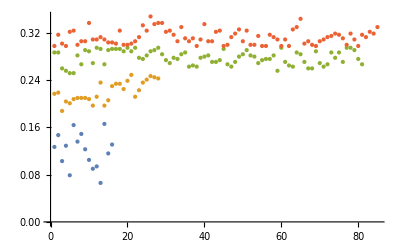

```mathematica
ListPlot[FindClusters[trematode12S,4,Method->"KMeans"],PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.127,0.147,0.103,0.129,0.079,0.164,0.136,0.149,0.123,0.105,0.09,0.094,0.066,0.166,0.116,0.131}]
```

0.120313

```mathematica
StandardDeviation[{0.127,0.147,0.103,0.129,0.079,0.164,0.136,0.149,0.123,0.105,0.09,0.094,0.066,0.166,0.116,0.131}]
```

0.0292568

```mathematica
MinMax[{0.127,0.147,0.103,0.129,0.079,0.164,0.136,0.149,0.123,0.105,0.09,0.094,0.066,0.166,0.116,0.131}]
```

{0.066,0.166}

```mathematica
Mean[{0.217,0.219,0.188,0.204,0.201,0.208,0.21,0.21,0.21,0.208,0.197,0.212,0.236,0.197,0.206,0.23,0.234,0.234,0.225,0.239,0.249,0.212,0.223,0.236,0.241,0.247,0.245,0.243}]
```

0.22075

```mathematica
StandardDeviation[{0.217,0.219,0.188,0.204,0.201,0.208,0.21,0.21,0.21,0.208,0.197,0.212,0.236,0.197,0.206,0.23,0.234,0.234,0.225,0.239,0.249,0.212,0.223,0.236,0.241,0.247,0.245,0.243}]
```

0.0173944

```mathematica
MinMax[{0.217,0.219,0.188,0.204,0.201,0.208,0.21,0.21,0.21,0.208,0.197,0.212,0.236,0.197,0.206,0.23,0.234,0.234,0.225,0.239,0.249,0.212,0.223,0.236,0.241,0.247,0.245,0.243}]
```

{0.188,0.249}

```mathematica
Mean[{0.298,0.317,0.302,0.298,0.322,0.324,0.3,0.306,0.306,0.337,0.309,0.309,0.313,0.309,0.304,0.304,0.302,0.324,0.3,0.3,0.302,0.306,0.313,0.333,0.324,0.348,0.335,0.337,0.337,0.322,0.324,0.317,0.306,0.33,0.311,0.306,0.311,0.298,0.309,0.335,0.306,0.306,0.322,0.324,0.298,0.3,0.313,0.319,0.326,0.306,0.324,0.3,0.3,0.315,0.298,0.298,0.317,0.313,0.309,0.298,0.309,0.298,0.326,0.33,0.344,0.302,0.306,0.3,0.298,0.306,0.309,0.313,0.315,0.319,0.317,0.311,0.3,0.319,0.309,0.298,0.317,0.313,0.322,0.319,0.33}]
```

0.313059

```mathematica
StandardDeviation[{0.298,0.317,0.302,0.298,0.322,0.324,0.3,0.306,0.306,0.337,0.309,0.309,0.313,0.309,0.304,0.304,0.302,0.324,0.3,0.3,0.302,0.306,0.313,0.333,0.324,0.348,0.335,0.337,0.337,0.322,0.324,0.317,0.306,0.33,0.311,0.306,0.311,0.298,0.309,0.335,0.306,0.306,0.322,0.324,0.298,0.3,0.313,0.319,0.326,0.306,0.324,0.3,0.3,0.315,0.298,0.298,0.317,0.313,0.309,0.298,0.309,0.298,0.326,0.33,0.344,0.302,0.306,0.3,0.298,0.306,0.309,0.313,0.315,0.319,0.317,0.311,0.3,0.319,0.309,0.298,0.317,0.313,0.322,0.319,0.33}]
```

0.0122701

```mathematica
MinMax[{0.298,0.317,0.302,0.298,0.322,0.324,0.3,0.306,0.306,0.337,0.309,0.309,0.313,0.309,0.304,0.304,0.302,0.324,0.3,0.3,0.302,0.306,0.313,0.333,0.324,0.348,0.335,0.337,0.337,0.322,0.324,0.317,0.306,0.33,0.311,0.306,0.311,0.298,0.309,0.335,0.306,0.306,0.322,0.324,0.298,0.3,0.313,0.319,0.326,0.306,0.324,0.3,0.3,0.315,0.298,0.298,0.317,0.313,0.309,0.298,0.309,0.298,0.326,0.33,0.344,0.302,0.306,0.3,0.298,0.306,0.309,0.313,0.315,0.319,0.317,0.311,0.3,0.319,0.309,0.298,0.317,0.313,0.322,0.319,0.33}]
```

{0.298,0.348}

```mathematica
Mean[{0.287,0.287,0.26,0.256,0.252,0.252,0.282,0.267,0.291,0.289,0.269,0.295,0.293,0.267,0.291,0.293,0.293,0.293,0.289,0.295,0.289,0.295,0.278,0.276,0.282,0.289,0.291,0.295,0.284,0.274,0.269,0.278,0.276,0.284,0.287,0.263,0.265,0.263,0.278,0.28,0.282,0.271,0.271,0.274,0.293,0.267,0.263,0.271,0.28,0.284,0.291,0.282,0.28,0.269,0.274,0.276,0.276,0.282,0.256,0.295,0.271,0.265,0.263,0.287,0.284,0.271,0.26,0.26,0.289,0.269,0.263,0.267,0.287,0.278,0.287,0.271,0.295,0.295,0.291,0.276,0.267}]
```

0.278148

```mathematica
StandardDeviation[{0.287,0.287,0.26,0.256,0.252,0.252,0.282,0.267,0.291,0.289,0.269,0.295,0.293,0.267,0.291,0.293,0.293,0.293,0.289,0.295,0.289,0.295,0.278,0.276,0.282,0.289,0.291,0.295,0.284,0.274,0.269,0.278,0.276,0.284,0.287,0.263,0.265,0.263,0.278,0.28,0.282,0.271,0.271,0.274,0.293,0.267,0.263,0.271,0.28,0.284,0.291,0.282,0.28,0.269,0.274,0.276,0.276,0.282,0.256,0.295,0.271,0.265,0.263,0.287,0.284,0.271,0.26,0.26,0.289,0.269,0.263,0.267,0.287,0.278,0.287,0.271,0.295,0.295,0.291,0.276,0.267}]
```

0.0119186

```mathematica
MinMax[{0.287,0.287,0.26,0.256,0.252,0.252,0.282,0.267,0.291,0.289,0.269,0.295,0.293,0.267,0.291,0.293,0.293,0.293,0.289,0.295,0.289,0.295,0.278,0.276,0.282,0.289,0.291,0.295,0.284,0.274,0.269,0.278,0.276,0.284,0.287,0.263,0.265,0.263,0.278,0.28,0.282,0.271,0.271,0.274,0.293,0.267,0.263,0.271,0.28,0.284,0.291,0.282,0.28,0.269,0.274,0.276,0.276,0.282,0.256,0.295,0.271,0.265,0.263,0.287,0.284,0.271,0.26,0.26,0.289,0.269,0.263,0.267,0.287,0.278,0.287,0.271,0.295,0.295,0.291,0.276,0.267}]
```

{0.252,0.295}

```mathematica
FindClusters[trematode16S,4,Method->"KMeans"]
```

{{0.144,0.101,0.08,0.143,0.147,0.113,0.122,0.129,0.071,0.107,0.113,0.147,0.14},{0.151,0.162,0.155,0.18,0.174,0.162,0.201,0.166,0.169,0.153,0.162,0.206,0.215,0.215,0.195,0.195,0.209,0.2},{0.259,0.24,0.269,0.258,0.246,0.233,0.24,0.231,0.242,0.235,0.253,0.241,0.25,0.251,0.26,0.242,0.247,0.246,0.231,0.24,0.272,0.269,0.263,0.278,0.278,0.271,0.269,0.278,0.28,0.269,0.271,0.256,0.268,0.264,0.277,0.271,0.263,0.265,0.254,0.253,0.258,0.268,0.26,0.263,0.251,0.271,0.276,0.263,0.274,0.268,0.278,0.259,0.251,0.255,0.264,0.274,0.276,0.265,0.269,0.268,0.28,0.276,0.242,0.247,0.262,0.263,0.276,0.274,0.268,0.277,0.265,0.276,0.272,0.28,0.277},{0.289,0.3,0.298,0.281,0.286,0.285,0.285,0.281,0.312,0.316,0.313,0.303,0.314,0.298,0.284,0.291,0.32,0.323,0.299,0.299,0.29,0.304,0.296,0.299,0.298,0.299,0.296,0.289,0.304,0.295,0.284,0.305,0.303,0.289,0.299,0.296,0.285,0.304,0.295,0.295,0.286,0.285,0.293,0.291,0.294,0.286,0.294,0.305,0.29,0.281,0.282,0.3,0.303,0.299,0.318,0.312,0.293,0.299,0.293,0.316,0.304,0.287,0.29,0.298,0.296,0.289,0.302,0.33,0.331,0.291,0.287,0.289,0.294,0.289,0.304,0.318,0.299,0.295,0.305,0.293,0.311,0.305,0.307,0.303,0.298,0.293,0.312,0.285,0.3,0.294,0.311,0.286,0.313,0.314,0.308,0.316,0.322,0.298,0.29,0.289,0.303,0.295,0.308,0.307}}

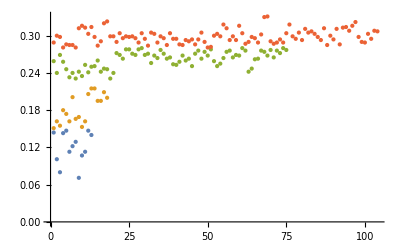

```mathematica
ListPlot[FindClusters[trematode16S,4,Method->"KMeans"],PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.144,0.101,0.08,0.143,0.147,0.113,0.122,0.129,0.071,0.107,0.113,0.147,0.14}]
```

0.119769

```mathematica
StandardDeviation[{0.144,0.101,0.08,0.143,0.147,0.113,0.122,0.129,0.071,0.107,0.113,0.147,0.14}]
```

0.0252921

```mathematica
MinMax[{0.144,0.101,0.08,0.143,0.147,0.113,0.122,0.129,0.071,0.107,0.113,0.147,0.14}]
```

{0.071,0.147}

```mathematica
Mean[{0.151,0.162,0.155,0.18,0.174,0.162,0.201,0.166,0.169,0.153,0.162,0.206,0.215,0.215,0.195,0.195,0.209,0.2}]
```

0.181667

```mathematica
StandardDeviation[{0.151,0.162,0.155,0.18,0.174,0.162,0.201,0.166,0.169,0.153,0.162,0.206,0.215,0.215,0.195,0.195,0.209,0.2}]
```

0.0226586

```mathematica
MinMax[{0.151,0.162,0.155,0.18,0.174,0.162,0.201,0.166,0.169,0.153,0.162,0.206,0.215,0.215,0.195,0.195,0.209,0.2}]
```

{0.151,0.215}

```mathematica
Mean[{0.237,0.23,0.21,0.216,0.246,0.244,0.249,0.233,0.228,0.233,0.248,0.238,0.24,0.256,0.243,0.261,0.257,0.244,0.26,0.231,0.24,0.231,0.244,0.246,0.233,0.242,0.213,0.263,0.261,0.265,0.258,0.269,0.266,0.27}]
```

0.244265

```mathematica
StandardDeviation[{0.237,0.23,0.21,0.216,0.246,0.244,0.249,0.233,0.228,0.233,0.248,0.238,0.24,0.256,0.243,0.261,0.257,0.244,0.26,0.231,0.24,0.231,0.244,0.246,0.233,0.242,0.213,0.263,0.261,0.265,0.258,0.269,0.266,0.27}]
```

0.0157178

```mathematica
MinMax[{0.237,0.23,0.21,0.216,0.246,0.244,0.249,0.233,0.228,0.233,0.248,0.238,0.24,0.256,0.243,0.261,0.257,0.244,0.26,0.231,0.24,0.231,0.244,0.246,0.233,0.242,0.213,0.263,0.261,0.265,0.258,0.269,0.266,0.27}]
```

{0.21,0.27}

```mathematica
Mean[{0.289,0.3,0.298,0.281,0.286,0.285,0.285,0.281,0.312,0.316,0.313,0.303,0.314,0.298,0.284,0.291,0.32,0.323,0.299,0.299,0.29,0.304,0.296,0.299,0.298,0.299,0.296,0.289,0.304,0.295,0.284,0.305,0.303,0.289,0.299,0.296,0.285,0.304,0.295,0.295,0.286,0.285,0.293,0.291,0.294,0.286,0.294,0.305,0.29,0.281,0.282,0.3,0.303,0.299,0.318,0.312,0.293,0.299,0.293,0.316,0.304,0.287,0.29,0.298,0.296,0.289,0.302,0.33,0.331,0.291,0.287,0.289,0.294,0.289,0.304,0.318,0.299,0.295,0.305,0.293,0.311,0.305,0.307,0.303,0.298,0.293,0.312,0.285,0.3,0.294,0.311,0.286,0.313,0.314,0.308,0.316,0.322,0.298,0.29,0.289,0.303,0.295,0.308,0.307}]
```

0.298856

```mathematica
StandardDeviation[{0.289,0.3,0.298,0.281,0.286,0.285,0.285,0.281,0.312,0.316,0.313,0.303,0.314,0.298,0.284,0.291,0.32,0.323,0.299,0.299,0.29,0.304,0.296,0.299,0.298,0.299,0.296,0.289,0.304,0.295,0.284,0.305,0.303,0.289,0.299,0.296,0.285,0.304,0.295,0.295,0.286,0.285,0.293,0.291,0.294,0.286,0.294,0.305,0.29,0.281,0.282,0.3,0.303,0.299,0.318,0.312,0.293,0.299,0.293,0.316,0.304,0.287,0.29,0.298,0.296,0.289,0.302,0.33,0.331,0.291,0.287,0.289,0.294,0.289,0.304,0.318,0.299,0.295,0.305,0.293,0.311,0.305,0.307,0.303,0.298,0.293,0.312,0.285,0.3,0.294,0.311,0.286,0.313,0.314,0.308,0.316,0.322,0.298,0.29,0.289,0.303,0.295,0.308,0.307}]
```

0.0110948

```mathematica
MinMax[{0.289,0.3,0.298,0.281,0.286,0.285,0.285,0.281,0.312,0.316,0.313,0.303,0.314,0.298,0.284,0.291,0.32,0.323,0.299,0.299,0.29,0.304,0.296,0.299,0.298,0.299,0.296,0.289,0.304,0.295,0.284,0.305,0.303,0.289,0.299,0.296,0.285,0.304,0.295,0.295,0.286,0.285,0.293,0.291,0.294,0.286,0.294,0.305,0.29,0.281,0.282,0.3,0.303,0.299,0.318,0.312,0.293,0.299,0.293,0.316,0.304,0.287,0.29,0.298,0.296,0.289,0.302,0.33,0.331,0.291,0.287,0.289,0.294,0.289,0.304,0.318,0.299,0.295,0.305,0.293,0.311,0.305,0.307,0.303,0.298,0.293,0.312,0.285,0.3,0.294,0.311,0.286,0.313,0.314,0.308,0.316,0.322,0.298,0.29,0.289,0.303,0.295,0.308,0.307}]
```

{0.281,0.331}

```mathematica
FindClusters[trematodeCOI,4,Method->"KMeans"]
```

{{0.176,0.165,0.154,0.171,0.089,0.133,0.125,0.166,0.141,0.139,0.142,0.092,0.108,0.164,0.159,0.16,0.169,0.177},{0.237,0.221,0.184,0.195,0.213,0.207,0.213,0.222,0.215,0.223,0.222,0.238,0.194,0.201,0.208,0.223,0.201,0.197,0.217,0.211,0.213,0.202,0.219,0.223,0.239,0.24,0.238},{0.242,0.268,0.27,0.264,0.272,0.255,0.273,0.26,0.264,0.282,0.281,0.281,0.281,0.282,0.282,0.268,0.267,0.27,0.245,0.255,0.262,0.282,0.253,0.264,0.252,0.279,0.268,0.277,0.278,0.268,0.265,0.272,0.267,0.253,0.259,0.251,0.282,0.274,0.283,0.272,0.264,0.264,0.271,0.271,0.26,0.281,0.268,0.27,0.249,0.252,0.268,0.276,0.243,0.246,0.262,0.272,0.274,0.278,0.252,0.255,0.249,0.278,0.278,0.275,0.254,0.262,0.25,0.278,0.277,0.277},{0.326,0.318,0.316,0.286,0.296,0.289,0.294,0.299,0.291,0.298,0.294,0.298,0.3,0.3,0.291,0.296,0.292,0.318,0.29,0.293,0.294,0.306,0.313,0.305,0.293,0.3,0.3,0.284,0.29,0.294,0.299,0.317,0.286,0.29,0.303,0.302,0.315,0.302,0.308,0.29,0.29,0.294,0.301,0.286,0.288,0.291,0.308,0.31,0.315,0.301,0.3,0.292,0.296,0.29,0.295,0.309,0.292,0.298,0.307,0.306,0.308,0.303,0.294,0.287,0.286,0.301,0.319,0.313,0.295,0.304,0.305,0.29,0.298,0.299,0.294,0.286,0.315,0.324,0.326,0.302,0.302,0.306,0.304,0.31,0.297,0.29,0.298,0.304,0.305,0.307,0.316,0.288,0.288,0.287,0.294}}

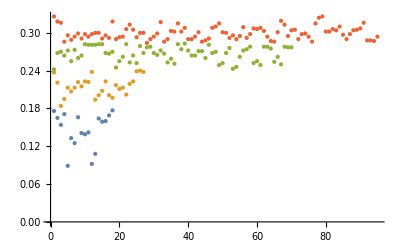

```mathematica
ListPlot[FindClusters[trematodeCOI,4,Method->"KMeans"],PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.176,0.165,0.154,0.171,0.089,0.133,0.125,0.166,0.141,0.139,0.142,0.092,0.108,0.164,0.159,0.16,0.169,0.177}]
```

0.146111

```mathematica
StandardDeviation[{0.176,0.165,0.154,0.171,0.089,0.133,0.125,0.166,0.141,0.139,0.142,0.092,0.108,0.164,0.159,0.16,0.169,0.177}]
```

0.0274802

```mathematica
MinMax[{0.176,0.165,0.154,0.171,0.089,0.133,0.125,0.166,0.141,0.139,0.142,0.092,0.108,0.164,0.159,0.16,0.169,0.177}]
```

{0.089,0.177}

```mathematica
Mean[{0.237,0.221,0.184,0.195,0.213,0.207,0.213,0.222,0.215,0.223,0.222,0.238,0.194,0.201,0.208,0.223,0.201,0.197,0.217,0.211,0.213,0.202,0.219,0.223,0.239,0.24,0.238}]
```

0.215407

```mathematica
StandardDeviation[{0.237,0.221,0.184,0.195,0.213,0.207,0.213,0.222,0.215,0.223,0.222,0.238,0.194,0.201,0.208,0.223,0.201,0.197,0.217,0.211,0.213,0.202,0.219,0.223,0.239,0.24,0.238}]
```

0.0150799

```mathematica
MinMax[{0.237,0.221,0.184,0.195,0.213,0.207,0.213,0.222,0.215,0.223,0.222,0.238,0.194,0.201,0.208,0.223,0.201,0.197,0.217,0.211,0.213,0.202,0.219,0.223,0.239,0.24,0.238}]
```

{0.184,0.24}

```mathematica
Mean[{0.242,0.268,0.27,0.264,0.272,0.255,0.273,0.26,0.264,0.282,0.281,0.281,0.281,0.282,0.282,0.268,0.267,0.27,0.245,0.255,0.262,0.282,0.253,0.264,0.252,0.279,0.268,0.277,0.278,0.268,0.265,0.272,0.267,0.253,0.259,0.251,0.282,0.274,0.283,0.272,0.264,0.264,0.271,0.271,0.26,0.281,0.268,0.27,0.249,0.252,0.268,0.276,0.243,0.246,0.262,0.272,0.274,0.278,0.252,0.255,0.249,0.278,0.278,0.275,0.254,0.262,0.25,0.278,0.277,0.277}]
```

0.266814

```mathematica
StandardDeviation[{0.242,0.268,0.27,0.264,0.272,0.255,0.273,0.26,0.264,0.282,0.281,0.281,0.281,0.282,0.282,0.268,0.267,0.27,0.245,0.255,0.262,0.282,0.253,0.264,0.252,0.279,0.268,0.277,0.278,0.268,0.265,0.272,0.267,0.253,0.259,0.251,0.282,0.274,0.283,0.272,0.264,0.264,0.271,0.271,0.26,0.281,0.268,0.27,0.249,0.252,0.268,0.276,0.243,0.246,0.262,0.272,0.274,0.278,0.252,0.255,0.249,0.278,0.278,0.275,0.254,0.262,0.25,0.278,0.277,0.277}]
```

0.0113754

```mathematica
MinMax[{0.242,0.268,0.27,0.264,0.272,0.255,0.273,0.26,0.264,0.282,0.281,0.281,0.281,0.282,0.282,0.268,0.267,0.27,0.245,0.255,0.262,0.282,0.253,0.264,0.252,0.279,0.268,0.277,0.278,0.268,0.265,0.272,0.267,0.253,0.259,0.251,0.282,0.274,0.283,0.272,0.264,0.264,0.271,0.271,0.26,0.281,0.268,0.27,0.249,0.252,0.268,0.276,0.243,0.246,0.262,0.272,0.274,0.278,0.252,0.255,0.249,0.278,0.278,0.275,0.254,0.262,0.25,0.278,0.277,0.277}]
```

{0.242,0.283}

```mathematica
Mean[{0.326,0.318,0.316,0.286,0.296,0.289,0.294,0.299,0.291,0.298,0.294,0.298,0.3,0.3,0.291,0.296,0.292,0.318,0.29,0.293,0.294,0.306,0.313,0.305,0.293,0.3,0.3,0.284,0.29,0.294,0.299,0.317,0.286,0.29,0.303,0.302,0.315,0.302,0.308,0.29,0.29,0.294,0.301,0.286,0.288,0.291,0.308,0.31,0.315,0.301,0.3,0.292,0.296,0.29,0.295,0.309,0.292,0.298,0.307,0.306,0.308,0.303,0.294,0.287,0.286,0.301,0.319,0.313,0.295,0.304,0.305,0.29,0.298,0.299,0.294,0.286,0.315,0.324,0.326,0.302,0.302,0.306,0.304,0.31,0.297,0.29,0.298,0.304,0.305,0.307,0.316,0.288,0.288,0.287,0.294}]
```

0.299895

```mathematica
StandardDeviation[{0.326,0.318,0.316,0.286,0.296,0.289,0.294,0.299,0.291,0.298,0.294,0.298,0.3,0.3,0.291,0.296,0.292,0.318,0.29,0.293,0.294,0.306,0.313,0.305,0.293,0.3,0.3,0.284,0.29,0.294,0.299,0.317,0.286,0.29,0.303,0.302,0.315,0.302,0.308,0.29,0.29,0.294,0.301,0.286,0.288,0.291,0.308,0.31,0.315,0.301,0.3,0.292,0.296,0.29,0.295,0.309,0.292,0.298,0.307,0.306,0.308,0.303,0.294,0.287,0.286,0.301,0.319,0.313,0.295,0.304,0.305,0.29,0.298,0.299,0.294,0.286,0.315,0.324,0.326,0.302,0.302,0.306,0.304,0.31,0.297,0.29,0.298,0.304,0.305,0.307,0.316,0.288,0.288,0.287,0.294}]
```

0.0100355

```mathematica
MinMax[{0.326,0.318,0.316,0.286,0.296,0.289,0.294,0.299,0.291,0.298,0.294,0.298,0.3,0.3,0.291,0.296,0.292,0.318,0.29,0.293,0.294,0.306,0.313,0.305,0.293,0.3,0.3,0.284,0.29,0.294,0.299,0.317,0.286,0.29,0.303,0.302,0.315,0.302,0.308,0.29,0.29,0.294,0.301,0.286,0.288,0.291,0.308,0.31,0.315,0.301,0.3,0.292,0.296,0.29,0.295,0.309,0.292,0.298,0.307,0.306,0.308,0.303,0.294,0.287,0.286,0.301,0.319,0.313,0.295,0.304,0.305,0.29,0.298,0.299,0.294,0.286,0.315,0.324,0.326,0.302,0.302,0.306,0.304,0.31,0.297,0.29,0.298,0.304,0.305,0.307,0.316,0.288,0.288,0.287,0.294}]
```

{0.284,0.326}

```mathematica
FindClusters[trematodeCOII,4,Method->"KMeans"]
```

{{0.179,0.204,0.177,0.161,0.113,0.179,0.17,0.183,0.208,0.183,0.177,0.149,0.165,0.159,0.217,0.19,0.181,0.192,0.194,0.217,0.199,0.199,0.185,0.226},{0.349,0.339,0.36,0.337,0.337,0.355,0.348,0.371,0.366,0.38,0.38,0.366,0.36,0.384,0.378,0.366,0.378,0.367,0.376,0.357,0.351,0.353,0.371,0.387,0.38,0.382,0.375,0.371,0.373,0.385,0.378,0.36,0.38,0.384,0.385,0.384,0.384,0.375,0.382,0.369,0.384,0.376,0.375,0.373,0.371,0.358,0.387,0.385,0.384,0.362,0.369,0.38,0.385,0.364,0.348,0.384,0.367,0.378,0.357,0.362,0.337,0.385,0.384,0.387,0.384,0.375,0.387,0.376,0.384,0.387,0.371,0.375,0.366,0.384,0.371,0.382,0.369,0.36,0.367,0.387,0.366,0.353,0.36,0.376,0.387,0.384,0.36,0.362,0.371,0.385,0.371,0.369,0.346,0.369},{0.299,0.326,0.292,0.317,0.303,0.328,0.294,0.328,0.314,0.289,0.333,0.281,0.274,0.285,0.296,0.292,0.294,0.303,0.303,0.29},{0.409,0.414,0.427,0.396,0.414,0.394,0.394,0.409,0.391,0.407,0.391,0.409,0.391,0.401,0.403,0.391,0.392,0.4,0.409,0.389,0.392,0.41,0.392,0.403,0.4,0.391,0.391,0.419,0.419,0.428,0.401,0.396,0.425,0.421,0.418,0.419,0.419,0.419,0.412,0.416,0.41,0.425,0.412,0.391,0.401,0.405,0.419,0.4,0.398,0.391,0.389,0.421,0.412,0.398,0.398,0.432,0.405,0.412,0.401,0.392,0.423,0.418,0.394,0.407,0.4,0.403,0.396,0.409,0.418,0.407,0.391,0.392}}

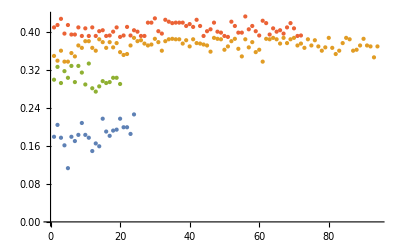

```mathematica
ListPlot[FindClusters[trematodeCOII,4,Method->"KMeans"],PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.179,0.204,0.177,0.161,0.113,0.179,0.17,0.183,0.208,0.183,0.177,0.149,0.165,0.159,0.217,0.19,0.181,0.192,0.194,0.217,0.199,0.199,0.185,0.226}]
```

0.183625

```mathematica
StandardDeviation[{0.179,0.204,0.177,0.161,0.113,0.179,0.17,0.183,0.208,0.183,0.177,0.149,0.165,0.159,0.217,0.19,0.181,0.192,0.194,0.217,0.199,0.199,0.185,0.226}]
```

0.0244074

```mathematica
MinMax[{0.179,0.204,0.177,0.161,0.113,0.179,0.17,0.183,0.208,0.183,0.177,0.149,0.165,0.159,0.217,0.19,0.181,0.192,0.194,0.217,0.199,0.199,0.185,0.226}]
```

{0.113,0.226}

```mathematica
Mean[{0.299,0.326,0.292,0.317,0.303,0.328,0.294,0.328,0.314,0.289,0.333,0.281,0.274,0.285,0.296,0.292,0.294,0.303,0.303,0.29}]
```

0.30205

```mathematica
StandardDeviation[{0.299,0.326,0.292,0.317,0.303,0.328,0.294,0.328,0.314,0.289,0.333,0.281,0.274,0.285,0.296,0.292,0.294,0.303,0.303,0.29}]
```

0.0169534

```mathematica
MinMax[{0.299,0.326,0.292,0.317,0.303,0.328,0.294,0.328,0.314,0.289,0.333,0.281,0.274,0.285,0.296,0.292,0.294,0.303,0.303,0.29}]
```

{0.274,0.333}

```mathematica
Mean[{0.349,0.339,0.36,0.337,0.337,0.355,0.348,0.371,0.366,0.38,0.38,0.366,0.36,0.384,0.378,0.366,0.378,0.367,0.376,0.357,0.351,0.353,0.371,0.387,0.38,0.382,0.375,0.371,0.373,0.385,0.378,0.36,0.38,0.384,0.385,0.384,0.384,0.375,0.382,0.369,0.384,0.376,0.375,0.373,0.371,0.358,0.387,0.385,0.384,0.362,0.369,0.38,0.385,0.364,0.348,0.384,0.367,0.378,0.357,0.362,0.337,0.385,0.384,0.387,0.384,0.375,0.387,0.376,0.384,0.387,0.371,0.375,0.366,0.384,0.371,0.382,0.369,0.36,0.367,0.387,0.366,0.353,0.36,0.376,0.387,0.384,0.36,0.362,0.371,0.385,0.371,0.369,0.346,0.369}]
```

0.37116

```mathematica
StandardDeviation[{0.349,0.339,0.36,0.337,0.337,0.355,0.348,0.371,0.366,0.38,0.38,0.366,0.36,0.384,0.378,0.366,0.378,0.367,0.376,0.357,0.351,0.353,0.371,0.387,0.38,0.382,0.375,0.371,0.373,0.385,0.378,0.36,0.38,0.384,0.385,0.384,0.384,0.375,0.382,0.369,0.384,0.376,0.375,0.373,0.371,0.358,0.387,0.385,0.384,0.362,0.369,0.38,0.385,0.364,0.348,0.384,0.367,0.378,0.357,0.362,0.337,0.385,0.384,0.387,0.384,0.375,0.387,0.376,0.384,0.387,0.371,0.375,0.366,0.384,0.371,0.382,0.369,0.36,0.367,0.387,0.366,0.353,0.36,0.376,0.387,0.384,0.36,0.362,0.371,0.385,0.371,0.369,0.346,0.369}]
```

0.0130675

```mathematica
MinMax[{0.349,0.339,0.36,0.337,0.337,0.355,0.348,0.371,0.366,0.38,0.38,0.366,0.36,0.384,0.378,0.366,0.378,0.367,0.376,0.357,0.351,0.353,0.371,0.387,0.38,0.382,0.375,0.371,0.373,0.385,0.378,0.36,0.38,0.384,0.385,0.384,0.384,0.375,0.382,0.369,0.384,0.376,0.375,0.373,0.371,0.358,0.387,0.385,0.384,0.362,0.369,0.38,0.385,0.364,0.348,0.384,0.367,0.378,0.357,0.362,0.337,0.385,0.384,0.387,0.384,0.375,0.387,0.376,0.384,0.387,0.371,0.375,0.366,0.384,0.371,0.382,0.369,0.36,0.367,0.387,0.366,0.353,0.36,0.376,0.387,0.384,0.36,0.362,0.371,0.385,0.371,0.369,0.346,0.369}]
```

{0.337,0.387}

```mathematica
Mean[{0.409,0.414,0.427,0.396,0.414,0.394,0.394,0.409,0.391,0.407,0.391,0.409,0.391,0.401,0.403,0.391,0.392,0.4,0.409,0.389,0.392,0.41,0.392,0.403,0.4,0.391,0.391,0.419,0.419,0.428,0.401,0.396,0.425,0.421,0.418,0.419,0.419,0.419,0.412,0.416,0.41,0.425,0.412,0.391,0.401,0.405,0.419,0.4,0.398,0.391,0.389,0.421,0.412,0.398,0.398,0.432,0.405,0.412,0.401,0.392,0.423,0.418,0.394,0.407,0.4,0.403,0.396,0.409,0.418,0.407,0.391,0.392}]
```

0.405444

```mathematica
StandardDeviation[{0.409,0.414,0.427,0.396,0.414,0.394,0.394,0.409,0.391,0.407,0.391,0.409,0.391,0.401,0.403,0.391,0.392,0.4,0.409,0.389,0.392,0.41,0.392,0.403,0.4,0.391,0.391,0.419,0.419,0.428,0.401,0.396,0.425,0.421,0.418,0.419,0.419,0.419,0.412,0.416,0.41,0.425,0.412,0.391,0.401,0.405,0.419,0.4,0.398,0.391,0.389,0.421,0.412,0.398,0.398,0.432,0.405,0.412,0.401,0.392,0.423,0.418,0.394,0.407,0.4,0.403,0.396,0.409,0.418,0.407,0.391,0.392}]
```

0.0116991

```mathematica
MinMax[{0.409,0.414,0.427,0.396,0.414,0.394,0.394,0.409,0.391,0.407,0.391,0.409,0.391,0.401,0.403,0.391,0.392,0.4,0.409,0.389,0.392,0.41,0.392,0.403,0.4,0.391,0.391,0.419,0.419,0.428,0.401,0.396,0.425,0.421,0.418,0.419,0.419,0.419,0.412,0.416,0.41,0.425,0.412,0.391,0.401,0.405,0.419,0.4,0.398,0.391,0.389,0.421,0.412,0.398,0.398,0.432,0.405,0.412,0.401,0.392,0.423,0.418,0.394,0.407,0.4,0.403,0.396,0.409,0.418,0.407,0.391,0.392}]
```

{0.389,0.432}

```mathematica
FindClusters[trematodecytb,4,Method->"KMeans"]
```

{{0.186,0.172,0.144,0.176,0.08,0.168,0.158,0.185,0.162,0.162,0.164,0.108,0.181,0.149,0.143},{0.246,0.256,0.248,0.254,0.276,0.243,0.258,0.255,0.25,0.251,0.261,0.262,0.257,0.267,0.266,0.257,0.268,0.245,0.27,0.276,0.272,0.248,0.252,0.25,0.258,0.263,0.251,0.277,0.275,0.276,0.254,0.271,0.25,0.246,0.246,0.273,0.256,0.271,0.251,0.279,0.248,0.248,0.25,0.266,0.277,0.254,0.259,0.255,0.251,0.266,0.247,0.264,0.26,0.264,0.27,0.275,0.268,0.267,0.262,0.267,0.251,0.278,0.269,0.276,0.251,0.255,0.266,0.279,0.254,0.252,0.266,0.277,0.274,0.276,0.255,0.245,0.266,0.264,0.266,0.269,0.25,0.26,0.26,0.264,0.262,0.263,0.253,0.271,0.279,0.278,0.25,0.256,0.265,0.264,0.274},{0.239,0.22,0.229,0.223,0.217,0.203,0.205,0.196,0.198,0.219,0.221,0.227,0.238,0.228,0.203,0.207,0.216,0.213,0.208,0.214,0.226,0.202,0.23,0.241,0.237,0.234,0.239,0.226,0.238,0.238},{0.289,0.311,0.306,0.323,0.286,0.281,0.294,0.297,0.282,0.292,0.291,0.295,0.295,0.289,0.295,0.313,0.292,0.291,0.298,0.288,0.29,0.289,0.299,0.304,0.297,0.282,0.283,0.295,0.284,0.28,0.29,0.294,0.288,0.286,0.296,0.305,0.307,0.293,0.294,0.284,0.293,0.298,0.312,0.312,0.318,0.281,0.312,0.28,0.307,0.29,0.295,0.308,0.33,0.336,0.335,0.288,0.282,0.294,0.288,0.28,0.302,0.293,0.297,0.31,0.31,0.307,0.292,0.297,0.285,0.292}}

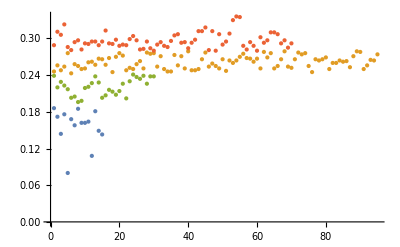

```mathematica
ListPlot[FindClusters[trematodecytb,4,Method->"KMeans"],PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.186,0.172,0.144,0.176,0.08,0.168,0.158,0.185,0.162,0.162,0.164,0.108,0.181,0.149,0.143}]
```

0.155867

```mathematica
StandardDeviation[{0.186,0.172,0.144,0.176,0.08,0.168,0.158,0.185,0.162,0.162,0.164,0.108,0.181,0.149,0.143}]
```

0.0289676

```mathematica
MinMax[{0.186,0.172,0.144,0.176,0.08,0.168,0.158,0.185,0.162,0.162,0.164,0.108,0.181,0.149,0.143}]
```

{0.08,0.186}

```mathematica
Mean[{0.239,0.22,0.229,0.223,0.217,0.203,0.205,0.196,0.198,0.219,0.221,0.227,0.238,0.228,0.203,0.207,0.216,0.213,0.208,0.214,0.226,0.202,0.23,0.241,0.237,0.234,0.239,0.226,0.238,0.238}]
```

0.221167

```mathematica
StandardDeviation[{0.239,0.22,0.229,0.223,0.217,0.203,0.205,0.196,0.198,0.219,0.221,0.227,0.238,0.228,0.203,0.207,0.216,0.213,0.208,0.214,0.226,0.202,0.23,0.241,0.237,0.234,0.239,0.226,0.238,0.238}]
```

0.0138541

```mathematica
MinMax[{0.239,0.22,0.229,0.223,0.217,0.203,0.205,0.196,0.198,0.219,0.221,0.227,0.238,0.228,0.203,0.207,0.216,0.213,0.208,0.214,0.226,0.202,0.23,0.241,0.237,0.234,0.239,0.226,0.238,0.238}]
```

{0.196,0.241}

```mathematica
Mean[{0.246,0.256,0.248,0.254,0.276,0.243,0.258,0.255,0.25,0.251,0.261,0.262,0.257,0.267,0.266,0.257,0.268,0.245,0.27,0.276,0.272,0.248,0.252,0.25,0.258,0.263,0.251,0.277,0.275,0.276,0.254,0.271,0.25,0.246,0.246,0.273,0.256,0.271,0.251,0.279,0.248,0.248,0.25,0.266,0.277,0.254,0.259,0.255,0.251,0.266,0.247,0.264,0.26,0.264,0.27,0.275,0.268,0.267,0.262,0.267,0.251,0.278,0.269,0.276,0.251,0.255,0.266,0.279,0.254,0.252,0.266,0.277,0.274,0.276,0.255,0.245,0.266,0.264,0.266,0.269,0.25,0.26,0.26,0.264,0.262,0.263,0.253,0.271,0.279,0.278,0.25,0.256,0.265,0.264,0.274}]
```

0.261484

```mathematica
StandardDeviation[{0.246,0.256,0.248,0.254,0.276,0.243,0.258,0.255,0.25,0.251,0.261,0.262,0.257,0.267,0.266,0.257,0.268,0.245,0.27,0.276,0.272,0.248,0.252,0.25,0.258,0.263,0.251,0.277,0.275,0.276,0.254,0.271,0.25,0.246,0.246,0.273,0.256,0.271,0.251,0.279,0.248,0.248,0.25,0.266,0.277,0.254,0.259,0.255,0.251,0.266,0.247,0.264,0.26,0.264,0.27,0.275,0.268,0.267,0.262,0.267,0.251,0.278,0.269,0.276,0.251,0.255,0.266,0.279,0.254,0.252,0.266,0.277,0.274,0.276,0.255,0.245,0.266,0.264,0.266,0.269,0.25,0.26,0.26,0.264,0.262,0.263,0.253,0.271,0.279,0.278,0.25,0.256,0.265,0.264,0.274}]
```

0.0102447

```mathematica
MinMax[{0.246,0.256,0.248,0.254,0.276,0.243,0.258,0.255,0.25,0.251,0.261,0.262,0.257,0.267,0.266,0.257,0.268,0.245,0.27,0.276,0.272,0.248,0.252,0.25,0.258,0.263,0.251,0.277,0.275,0.276,0.254,0.271,0.25,0.246,0.246,0.273,0.256,0.271,0.251,0.279,0.248,0.248,0.25,0.266,0.277,0.254,0.259,0.255,0.251,0.266,0.247,0.264,0.26,0.264,0.27,0.275,0.268,0.267,0.262,0.267,0.251,0.278,0.269,0.276,0.251,0.255,0.266,0.279,0.254,0.252,0.266,0.277,0.274,0.276,0.255,0.245,0.266,0.264,0.266,0.269,0.25,0.26,0.26,0.264,0.262,0.263,0.253,0.271,0.279,0.278,0.25,0.256,0.265,0.264,0.274}]
```

{0.243,0.279}

```mathematica
Mean[{0.289,0.311,0.306,0.323,0.286,0.281,0.294,0.297,0.282,0.292,0.291,0.295,0.295,0.289,0.295,0.313,0.292,0.291,0.298,0.288,0.29,0.289,0.299,0.304,0.297,0.282,0.283,0.295,0.284,0.28,0.29,0.294,0.288,0.286,0.296,0.305,0.307,0.293,0.294,0.284,0.293,0.298,0.312,0.312,0.318,0.281,0.312,0.28,0.307,0.29,0.295,0.308,0.33,0.336,0.335,0.288,0.282,0.294,0.288,0.28,0.302,0.293,0.297,0.31,0.31,0.307,0.292,0.297,0.285,0.292}]
```

0.296743

```mathematica
StandardDeviation[{0.289,0.311,0.306,0.323,0.286,0.281,0.294,0.297,0.282,0.292,0.291,0.295,0.295,0.289,0.295,0.313,0.292,0.291,0.298,0.288,0.29,0.289,0.299,0.304,0.297,0.282,0.283,0.295,0.284,0.28,0.29,0.294,0.288,0.286,0.296,0.305,0.307,0.293,0.294,0.284,0.293,0.298,0.312,0.312,0.318,0.281,0.312,0.28,0.307,0.29,0.295,0.308,0.33,0.336,0.335,0.288,0.282,0.294,0.288,0.28,0.302,0.293,0.297,0.31,0.31,0.307,0.292,0.297,0.285,0.292}]
```

0.0127355

```mathematica
MinMax[{0.289,0.311,0.306,0.323,0.286,0.281,0.294,0.297,0.282,0.292,0.291,0.295,0.295,0.289,0.295,0.313,0.292,0.291,0.298,0.288,0.29,0.289,0.299,0.304,0.297,0.282,0.283,0.295,0.284,0.28,0.29,0.294,0.288,0.286,0.296,0.305,0.307,0.293,0.294,0.284,0.293,0.298,0.312,0.312,0.318,0.281,0.312,0.28,0.307,0.29,0.295,0.308,0.33,0.336,0.335,0.288,0.282,0.294,0.288,0.28,0.302,0.293,0.297,0.31,0.31,0.307,0.292,0.297,0.285,0.292}]
```

{0.28,0.336}

```mathematica
FindClusters[trematodeND,4,Method->"KMeans"]
```

{{0.205,0.19,0.236,0.243,0.24,0.229,0.204,0.21,0.204,0.2,0.224,0.19,0.254,0.209,0.203,0.217,0.222,0.198,0.215,0.211,0.209,0.241,0.243,0.248,0.253,0.253},{0.157,0.185,0.083,0.141,0.141,0.184,0.167,0.172,0.119,0.131,0.172,0.174},{0.287,0.302,0.285,0.269,0.297,0.293,0.308,0.292,0.292,0.281,0.288,0.294,0.309,0.265,0.281,0.287,0.282,0.293,0.309,0.304,0.291,0.291,0.292,0.304,0.313,0.306,0.29,0.287,0.259,0.271,0.284,0.281,0.313,0.297,0.299,0.279,0.28,0.269,0.265,0.29,0.279,0.313,0.31,0.309,0.312,0.288,0.308,0.287,0.291,0.292,0.312,0.309,0.257,0.266,0.311,0.277,0.265,0.309,0.296,0.282,0.282,0.275,0.271,0.273,0.313,0.294,0.277,0.282,0.308,0.291,0.29,0.294,0.291,0.278,0.311,0.313,0.312,0.288,0.282,0.286,0.29,0.278,0.271,0.292,0.275,0.297,0.31,0.303,0.29,0.287,0.278,0.292,0.277,0.281,0.287,0.287,0.281,0.308,0.302,0.298,0.291,0.287,0.305,0.29,0.286},{0.386,0.383,0.377,0.335,0.348,0.329,0.334,0.335,0.316,0.346,0.344,0.338,0.341,0.348,0.331,0.359,0.335,0.338,0.338,0.333,0.353,0.331,0.327,0.327,0.347,0.356,0.329,0.348,0.334,0.338,0.319,0.364,0.344,0.342,0.321,0.318,0.316,0.317,0.344,0.33,0.323,0.354,0.318,0.377,0.356,0.355,0.329,0.337,0.323,0.321,0.331,0.322,0.318,0.316,0.384,0.341,0.337,0.333,0.373,0.34,0.333,0.328,0.317,0.315,0.317,0.343,0.322}}

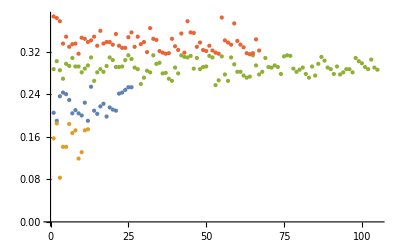

```mathematica
ListPlot[FindClusters[trematodeND,4,Method->"KMeans"],PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.157,0.185,0.083,0.141,0.141,0.184,0.167,0.172,0.119,0.131,0.172,0.174}]
```

0.152167

```mathematica
StandardDeviation[{0.157,0.185,0.083,0.141,0.141,0.184,0.167,0.172,0.119,0.131,0.172,0.174}]
```

0.0304208

```mathematica
MinMax[{0.157,0.185,0.083,0.141,0.141,0.184,0.167,0.172,0.119,0.131,0.172,0.174}]
```

{0.083,0.185}

```mathematica
Mean[{0.205,0.19,0.236,0.243,0.24,0.229,0.204,0.21,0.204,0.2,0.224,0.19,0.254,0.209,0.203,0.217,0.222,0.198,0.215,0.211,0.209,0.241,0.243,0.248,0.253,0.253}]
```

0.221192

```mathematica
StandardDeviation[{0.205,0.19,0.236,0.243,0.24,0.229,0.204,0.21,0.204,0.2,0.224,0.19,0.254,0.209,0.203,0.217,0.222,0.198,0.215,0.211,0.209,0.241,0.243,0.248,0.253,0.253}]
```

0.0204978

```mathematica
MinMax[{0.205,0.19,0.236,0.243,0.24,0.229,0.204,0.21,0.204,0.2,0.224,0.19,0.254,0.209,0.203,0.217,0.222,0.198,0.215,0.211,0.209,0.241,0.243,0.248,0.253,0.253}]
```

{0.19,0.254}

```mathematica
Mean[{0.287,0.302,0.285,0.269,0.297,0.293,0.308,0.292,0.292,0.281,0.288,0.294,0.309,0.265,0.281,0.287,0.282,0.293,0.309,0.304,0.291,0.291,0.292,0.304,0.313,0.306,0.29,0.287,0.259,0.271,0.284,0.281,0.313,0.297,0.299,0.279,0.28,0.269,0.265,0.29,0.279,0.313,0.31,0.309,0.312,0.288,0.308,0.287,0.291,0.292,0.312,0.309,0.257,0.266,0.311,0.277,0.265,0.309,0.296,0.282,0.282,0.275,0.271,0.273,0.313,0.294,0.277,0.282,0.308,0.291,0.29,0.294,0.291,0.278,0.311,0.313,0.312,0.288,0.282,0.286,0.29,0.278,0.271,0.292,0.275,0.297,0.31,0.303,0.29,0.287,0.278,0.292,0.277,0.281,0.287,0.287,0.281,0.308,0.302,0.298,0.291,0.287,0.305,0.29,0.286}]
```

0.290533

```mathematica
StandardDeviation[{0.287,0.302,0.285,0.269,0.297,0.293,0.308,0.292,0.292,0.281,0.288,0.294,0.309,0.265,0.281,0.287,0.282,0.293,0.309,0.304,0.291,0.291,0.292,0.304,0.313,0.306,0.29,0.287,0.259,0.271,0.284,0.281,0.313,0.297,0.299,0.279,0.28,0.269,0.265,0.29,0.279,0.313,0.31,0.309,0.312,0.288,0.308,0.287,0.291,0.292,0.312,0.309,0.257,0.266,0.311,0.277,0.265,0.309,0.296,0.282,0.282,0.275,0.271,0.273,0.313,0.294,0.277,0.282,0.308,0.291,0.29,0.294,0.291,0.278,0.311,0.313,0.312,0.288,0.282,0.286,0.29,0.278,0.271,0.292,0.275,0.297,0.31,0.303,0.29,0.287,0.278,0.292,0.277,0.281,0.287,0.287,0.281,0.308,0.302,0.298,0.291,0.287,0.305,0.29,0.286}]
```

0.0138648

```mathematica
MinMax[{0.287,0.302,0.285,0.269,0.297,0.293,0.308,0.292,0.292,0.281,0.288,0.294,0.309,0.265,0.281,0.287,0.282,0.293,0.309,0.304,0.291,0.291,0.292,0.304,0.313,0.306,0.29,0.287,0.259,0.271,0.284,0.281,0.313,0.297,0.299,0.279,0.28,0.269,0.265,0.29,0.279,0.313,0.31,0.309,0.312,0.288,0.308,0.287,0.291,0.292,0.312,0.309,0.257,0.266,0.311,0.277,0.265,0.309,0.296,0.282,0.282,0.275,0.271,0.273,0.313,0.294,0.277,0.282,0.308,0.291,0.29,0.294,0.291,0.278,0.311,0.313,0.312,0.288,0.282,0.286,0.29,0.278,0.271,0.292,0.275,0.297,0.31,0.303,0.29,0.287,0.278,0.292,0.277,0.281,0.287,0.287,0.281,0.308,0.302,0.298,0.291,0.287,0.305,0.29,0.286}]
```

{0.257,0.313}

```mathematica
Mean[{0.386,0.383,0.377,0.335,0.348,0.329,0.334,0.335,0.316,0.346,0.344,0.338,0.341,0.348,0.331,0.359,0.335,0.338,0.338,0.333,0.353,0.331,0.327,0.327,0.347,0.356,0.329,0.348,0.334,0.338,0.319,0.364,0.344,0.342,0.321,0.318,0.316,0.317,0.344,0.33,0.323,0.354,0.318,0.377,0.356,0.355,0.329,0.337,0.323,0.321,0.331,0.322,0.318,0.316,0.384,0.341,0.337,0.333,0.373,0.34,0.333,0.328,0.317,0.315,0.317,0.343,0.322}]
```

0.338239

```mathematica
StandardDeviation[{0.386,0.383,0.377,0.335,0.348,0.329,0.334,0.335,0.316,0.346,0.344,0.338,0.341,0.348,0.331,0.359,0.335,0.338,0.338,0.333,0.353,0.331,0.327,0.327,0.347,0.356,0.329,0.348,0.334,0.338,0.319,0.364,0.344,0.342,0.321,0.318,0.316,0.317,0.344,0.33,0.323,0.354,0.318,0.377,0.356,0.355,0.329,0.337,0.323,0.321,0.331,0.322,0.318,0.316,0.384,0.341,0.337,0.333,0.373,0.34,0.333,0.328,0.317,0.315,0.317,0.343,0.322}]
```

0.0179208

```mathematica
MinMax[{0.386,0.383,0.377,0.335,0.348,0.329,0.334,0.335,0.316,0.346,0.344,0.338,0.341,0.348,0.331,0.359,0.335,0.338,0.338,0.333,0.353,0.331,0.327,0.327,0.347,0.356,0.329,0.348,0.334,0.338,0.319,0.364,0.344,0.342,0.321,0.318,0.316,0.317,0.344,0.33,0.323,0.354,0.318,0.377,0.356,0.355,0.329,0.337,0.323,0.321,0.331,0.322,0.318,0.316,0.384,0.341,0.337,0.333,0.373,0.34,0.333,0.328,0.317,0.315,0.317,0.343,0.322}]
```

{0.315,0.386}